```mathematica
S[x_]:=4/(Sqrt[Pi W])Exp[-x^2/W]
Subscript[k, w][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](x-ξ)],x<ξ}}]
Subscript[k, l][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](x-ξ)],x<ξ}}]
var=Rationalize[{Subscript[α, w]->50.58,Subscript[β, w]->3.85/0.38,Subscript[η, w]->1/(0.38*10)*Q,Subscript[α, l]->192.2/(1.89*10),Subscript[β, l]->3.85/1.89,Subscript[η, l]->1/(1.89*10)*Q,Subscript[a, 0]->0.6,Subscript[a, 1]->0.38,M->0.38/1.89,Subscript[L, 0]->-1,Subscript[L, 1]->1}];
```

```mathematica
Subscript[T, 0][ξ_]:=Limit[Subscript[c, 0] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ<Subscript[A, 0]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,-∞,Subscript[A, 0]},Assumptions->ξ<Subscript[A, 0]<Subscript[L, 0]/.var]+Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,-∞,Subscript[A, 0]},Assumptions->{ξ<Subscript[A, 0]<Subscript[L, 0]/.var,W>0}]
Subscript[F, 0][ξ_]=Refine[Subscript[T, 0][ξ]/.var,{ξ<Subscript[A, 0]<Subscript[L, 0]}/.var];
```

```mathematica
Subscript[T, 1][ξ_]:=Limit[Subscript[c, 2] Subscript[k, w][x,ξ]-Subscript[c, 1] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 0],Assumptions->ξ<Subscript[L, 0]]-Limit[Subscript[c, 0] Subscript[k, w][x,ξ]+ D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ>Subscript[A, 0]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[A, 0],Subscript[L, 0]}/.var,Assumptions->{Subscript[A, 0]<ξ<Subscript[L, 0]/.var,Subscript[A, 0]<Subscript[L, 0]/.var}]+Subscript[η, w](1-Subscript[a, 1])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[A, 0],Subscript[L, 0]}/.var,Assumptions->{Subscript[A, 0]<ξ<Subscript[L, 0]/.var,Subscript[A, 0]<Subscript[L, 0]/.var,W>0}]
Subscript[F, 1][ξ_]=Refine[Subscript[T, 1][ξ]/.var,{Subscript[A, 0]<ξ<Subscript[L, 0]}/.var];
```

```mathematica
Subscript[T, 2][ξ_]:=Limit[M Subscript[c, 4] Subscript[k, l][x,ξ]-Subscript[c, 3] D[Subscript[k, l][x,ξ], x],x->Subscript[L, 1],Assumptions->ξ<Subscript[L, 1]]-Limit[M Subscript[c, 2] Subscript[k, l][x,ξ]-Subscript[c, 1] D[Subscript[k, l][x,ξ], x],x->Subscript[L, 0],Assumptions->ξ>Subscript[L, 0]]-Subscript[α, l] Integrate[Subscript[k, l][x,ξ],{x,Subscript[L, 0],Subscript[L, 1]}/.var,Assumptions->Subscript[L, 0]<ξ<Subscript[L, 1]/.var]+Subscript[η, l](1-Subscript[a, 0])Integrate[Subscript[k, l][x,ξ]S[x],{x,Subscript[L, 0],Subscript[L, 1]}/.var,Assumptions->{Subscript[L, 0]<ξ<Subscript[L, 1]/.var, W>0}]
Subscript[F, 2][ξ_]=Refine[Subscript[T, 2][ξ]/.var,{Subscript[L, 0]<ξ<Subscript[L, 1]/.var}];
```

```mathematica
Subscript[T, 3][ξ_]:=Limit[Subscript[c, 5] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 1],Assumptions->ξ<Subscript[A, 1]]-Limit[Subscript[c, 4] Subscript[k, w][x,ξ]-Subscript[c, 3] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 1],Assumptions->ξ>Subscript[L, 1]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[L, 1],Subscript[A, 1]}/.var,Assumptions->{Subscript[L, 1]<ξ<Subscript[A, 1]/.var,Subscript[L, 1]<Subscript[A, 1]/.var}]+Subscript[η, w](1-Subscript[a, 1])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[L, 1],Subscript[A, 1]}/.var,Assumptions->{Subscript[L, 1]<ξ<Subscript[A, 1]/.var,Subscript[L, 1]<Subscript[A, 1]/.var,W>0}]
Subscript[F, 3][ξ_]=Refine[Subscript[T, 3][ξ]/.var,{Subscript[L, 1]<ξ<Subscript[A, 1]}/.var];
```

```mathematica
Subscript[T, 4][ξ_]:=-Limit[Subscript[c, 5] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 1],Assumptions->ξ>Subscript[A, 1]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[A, 1],∞},Assumptions->ξ>Subscript[A, 1]>Subscript[L, 1]/.var]+Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[A, 1],∞},Assumptions->{ξ>Subscript[A, 1]>Subscript[L, 1]/.var,W>0}]
Subscript[F, 4][ξ_]=Refine[Subscript[T, 4][ξ]/.var,{Subscript[L, 1]<Subscript[A, 1]<ξ}/.var];
```

```mathematica
Subscript[eqn, 0]=Subscript[F, 0][Subscript[A, 0]]+1==0;
Subscript[eqn, 1]=Subscript[F, 1][Subscript[A, 0]]+1==0;
Subscript[eqn, 2]=Subscript[F, 3][Subscript[A, 1]]+1==0;
Subscript[eqn, 3]=Subscript[F, 4][Subscript[A, 1]]+1==0;
Subscript[eqn, 4]=Subscript[F, 1][Subscript[L, 0]]-Subscript[F, 2][Subscript[L, 0]]==0/.var;
Subscript[eqn, 5]=Subscript[F, 2][Subscript[L, 1]]-Subscript[F, 3][Subscript[L, 1]]==0/.var;
Subscript[eqn, 6]=Subscript[F, 2]'[Subscript[L, 0]]-M Subscript[F, 1]'[Subscript[L, 0]]==0/.var;
Subscript[eqn, 7]=Subscript[F, 2]'[Subscript[L, 1]]-M Subscript[F, 3]'[Subscript[L, 1]]==0/.var;
```

```mathematica
(*Finding what Q's has solution on this form*)
Subscript[Q, min]=472.23;
Subscript[Q, max]=472.23;
n=IntegerPart[2Abs[(Subscript[Q, max]-Subscript[Q, min])]+0.5]+1
(*n=1401;*)
Subscript[W, test]=6;
sols={};
Monitor[
For[i=0,i<n,i++,
tempQ={Q->Rationalize[Subscript[Q, min]+(Subscript[Q, max]-Subscript[Q, min])*i/(n-1),0],W->Rationalize[Subscript[W, test],0]};
sol=Quiet[FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5],Subscript[eqn, 6],Subscript[eqn, 7]}/.tempQ,{{Subscript[c, 0],Subscript[c, 0]/.sol},{Subscript[c, 1],Subscript[c, 1]/.sol},{Subscript[c, 2],Subscript[c, 2]/.sol},{Subscript[c, 3],Subscript[c, 3]/.sol},{Subscript[c, 4],Subscript[c, 4]/.sol},{Subscript[c, 5],Subscript[c, 5]/.sol},{Subscript[A, 0],Subscript[A, 0]/.sol},{Subscript[A, 1],Subscript[A, 1]/.sol}},MaxIterations->100,WorkingPrecision->30]];
sol=Join[sol,tempQ,var/.tempQ];
Quiet[conds=Subscript[F, 2][0]<0/.sol];
If[conds,M[x_]=Rationalize[Piecewise[{{Subscript[F, 0][x],x<=Subscript[A, 0]},{Subscript[F, 1][x],Subscript[A, 0]<x<Subscript[L, 0]},{Subscript[F, 2][x],Subscript[L, 0]<=x<=Subscript[L, 1]},{Subscript[F, 3][x],Subscript[L, 1]<x<Subscript[A, 1]},{Subscript[F, 4][x],Subscript[A, 1]<=x}}/.sol],0];
NUM=12001;
points=SetPrecision[Table[-6+12(i-1)/(NUM-1),{i,NUM}],20];
nSolution=N[Map[M, points]];
sols=Join[sols,{{N[Q/.sol],N[M[0]/.sol],nSolution}}],Nothing];
],{N[i/n],N[Q/.tempQ]}]
Beep[]
```

1

```mathematica
Export["C:\\masterA GitHub\\Code\\Gaussian\\Std 6\\2 - IceWaterSnowWaterIce_4.csv",sols,Format->Table];
```

```mathematica
472.0727355444
```

```mathematica
478.1207301537
```

```mathematica
522.61928
```

{c_0→2.67722913398930790855692987408,c_1→-0.78263704600443165202339503481,c_2→0.116178758582167760904207065329,c_3→-0.78263704600443165202339503481,c_4→-0.11617875858216776090420706533,c_5→-2.67722913398930790855692987408,A_0→-1.15416475010111840882643429483,A_1→1.15416475010111840882643429483}

-0.673120781667612988090940579446

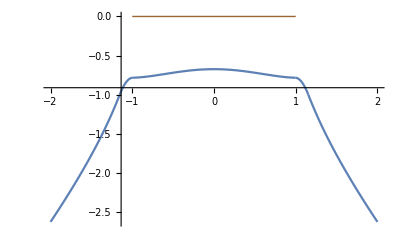

```mathematica
tempQ={Q->Rationalize[472.23,0],W->6};
usePrev=False;
If[usePrev,sol=FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5],Subscript[eqn, 6],Subscript[eqn, 7]}/.tempQ,{{Subscript[c, 0],Subscript[c, 0]/.sol},{Subscript[c, 1],Subscript[c, 1]/.sol},{Subscript[c, 2],Subscript[c, 2]/.sol},{Subscript[c, 3],Subscript[c, 3]/.sol},{Subscript[c, 4],Subscript[c, 4]/.sol},{Subscript[c, 5],Subscript[c, 5]/.sol},{Subscript[A, 0],Subscript[A, 0]/.sol},{Subscript[A, 1],Subscript[A, 1]/.sol}},MaxIterations->100,WorkingPrecision->30],
sol=FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5],Subscript[eqn, 6],Subscript[eqn, 7]}/.tempQ,{{Subscript[c, 0],0},{Subscript[c, 1],0},{Subscript[c, 2],0},{Subscript[c, 3],0},{Subscript[c, 4],0},{Subscript[c, 5],0},{Subscript[A, 0],-1.1},{Subscript[A, 1],1.1}},MaxIterations->100,WorkingPrecision->30]]
sol=Rationalize[Join[sol,tempQ],0];
sol=Join[sol,var/.sol];
Subscript[p, 0]=Plot[Subscript[F, 0][x]/.sol,{x,-2,Subscript[A, 0]/.sol},PlotRange->All,WorkingPrecision->30];
Subscript[p, 1]=Plot[Subscript[F, 1][x]/.sol,{x,Subscript[A, 0]/.sol,Subscript[L, 0]/.sol},PlotRange->All,WorkingPrecision->30];
Subscript[p, 2]=Plot[Subscript[F, 2][x]/.sol,{x,Subscript[L, 0]/.sol,Subscript[L, 1]/.sol},PlotRange->All,WorkingPrecision->30];
Subscript[p, 3]=Plot[Subscript[F, 3][x]/.sol,{x,Subscript[L, 1]/.sol,Subscript[A, 1]/.sol},PlotRange->All,WorkingPrecision->30];
Subscript[p, 4]=Plot[Subscript[F, 4][x]/.sol,{x,Subscript[A, 1]/.sol,2},PlotRange->All,WorkingPrecision->30];
Subscript[p, 5]=Plot[0,{x,Subscript[L, 0],Subscript[L, 1]}/.sol,PlotRange->All,PlotStyle->{Brown,Thick}];
N[Subscript[F, 2][0]/.sol,30]
Show[Subscript[p, 0],Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[p, 5],PlotRange->All]
```